# Un tool per CCS

## Progetto di Matematica Computazionale

Federico Viscomi 577326

## Introduzione

### Introduzione

CCS (Calculus of communicating systems) e' un linguaggio usato per la modellazione e la verifica di sistemi reattivi e distribuiti, ad esempio:
- sistemi operativi
- protocolli in generale
- programmi di controllo di dispositivi con sensori e attuatori

In particolare grazie a ccs siamo in grado di:
- definire specifiche e implementazioni di sistemi
- dimostrare l'equivalenza di specifica e implementazione di un certo sistema 
- dimostrare l'equivalenza di sistemi
- dimostrare certe proprieta' di un sistema specificate ad esempio tramite la logica di Hennessy-Milner

[AIL07] fornisce una descrizione approfondita del CCS.

In questa presentazione esponiamo la sintassi e la semantica del linguaggio CCS e infine mostriamo il contenuto del pacchetto. In particolare questo pacchetto permette di calcolare la semantica di un processo CCS.

## CCS

### Sintassi del CCS

Supponiamo di avere un insieme Input di nomi che chiameremo nomi di input o semplicemente input e un insieme Identifier di nomi che chiameremo identificatori. Se a e’ un input allora indichiamo con :a l’output del nome a. Inoltre supponiamo di avere un nome tau che non sta ne in Input ne in Identifier. Definiamo il linguaggio CCS come il piu’ piccolo sottoinsieme di stringhe sull’alfabeto:
			(Input ∪ Identifier ∪ {.,+,|,/ ,0,:} ∪ parentesi tonde e quadre)
tale che’
- 0 ∈ CCS
- Identifier ⊆ CCS
- P ∈ CCS ∧ a ∈ Input ⇒ 
		a.P ∈ CCS 
		∧ :a.P ∈ CCS 
- P ∈ CCS ∧ {a_1, …,a_n} ⊆ Input ⇒
	 {a_1 … a_n}/P ∈ CCS
- P,Q ∈ CCS ⇒ 
	P+Q ∈ CCS 
	∧ P|Q ∈ CCS 
- P ∈ CCS ⇒
	(P) ∈ CCS

Usiamo il termine processo per riferirci ad una stringa del linguaggio CCS. Diamo i seguenti nomi agli operatori del CCS:
 + somma
  | composizione parallela
  / restrizione 
  . prefisso

Una definizione di un identificatore e’ 
					A = P
dove A e’ un identificatore e P e’ un processo CCS.

Gli operatori di composizione parallela e di somma hanno entrambi associtivita’ a sinistra ma l’operatore di composizione parallela ha priorita’ piu’ alta rispetto a quello di somma. Quindi ad esempio il processo 
					a.0 + b.0 | c.0
e’ uguale a
					a.0 + (b.0 | c.0)

### Semantica formale del CCS ed esempi di uso del package

La semantica di un processo P ∈ CCS e’ un grafo diretto etichettato cioe’ un grafo diretto e una funzione che associa stringhe ai suoi vertici. Rappresentiamo un grafo etichettato come {N, E} dove 
- N e’ l’insieme dei nodi. I nodi in questo caso sono processi CCS.
- E e’ l’insieme degli archi etichettati. Un elemento di E e’ una tripla:
			(nodo di partenza, etichetta dell’arco, nodo di arrivo).
 se (P,a,Q) ∈ E allora scriviamo P ⟶^a Q  ∈ E
  
L’etichetta di un arco puo’ essere un input, un output oppure tau. Di seguito indichiamo con le prime lettere dell’alfabeto in minuscolo a,b,c... un elemento di Input, con P e Q due processi CCS, mentre con label indichiamo: un elemento di Input, un output oppure tau. Diciamo che un processo fa un’azione quando: prende un nome in input, da un nome in output, fa l’azione tau. La semantica di un processo CCS e’ definita per induzione strutturale nel modo seguente:

la semantica del processo 0 e’ il grafo 
					{{0},ϕ}
rappresenta il processo terminato o nullo, cioe’ il processo che non puo’ agire.

la semantica del processo a.P e’ il grafo 
				{{(a.P)} ∪ N , {a.P ⟶^a P} ∪ E} 
dove {N,E} e’ la semantica del processo P. Ad esempio la semantica di a.0 e’ il grafo seguente

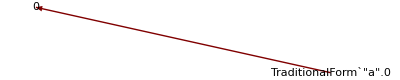

dalla semantica si nota che il processo a.0 puo’ prendere in input a e poi terminare.

la semantica del processo :a.P e’ il grafo 
				{{:a.P} ∪ N , {:a.P ⟶^(:a) P} ∪ E} 
dove {N,E} e’ la semantica del processo P. Ad esempio la semantica di :a.0 e’ il grafo seguente

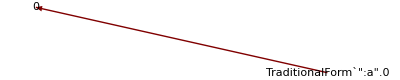

tale processo puo’ produrre a come output ed arrivare in 0.

la semantica del processo P+Q e’ il grafo
 	{({P+Q} ∪ N ∪ M) - {P,Q} , 
 		{P+Q⟶^labelR, dove P⟶^labelR ∈ E}
 		∪ {P+Q⟶^labelR dove Q⟶^labelR ∈ F}
  		∪ {(start, label, end)∈E tale che start e’ diverso da P}
  		∪ {(start, label, end)∈F tale che start e’ diverso da Q}}
dove {N,E} e’ la semantica del processo P e {M,F} e’ la semantica del processo Q. La somma di processi serve per rappresentare il non determinismo. In altre parole il processo P+Q si puo’ comportare o come P o come Q. Ad esempio la semantica di a.b.0 + c.d.0 e’ il grafo seguente

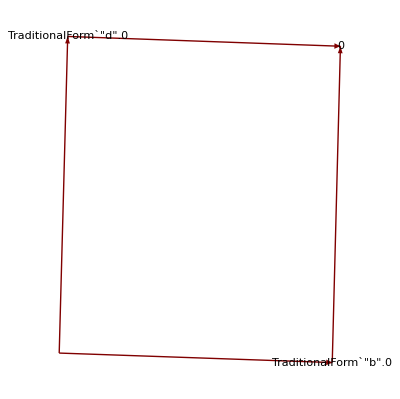

la semantica del processo P|Q e’ il grafo
	{{R|S, dove R∈ N e S ∈ M}, 
		{R|T⟶^labelS|T, dove R⟶^labelS ∈ E e T ∈ M} 
		∪ {T|R⟶^labelT|S, dove R⟶^labelS ∈ F e T ∈ N}}
dove {N,E} e’ la semantica del processo P e {M,F} e’ la semantica del processo Q. P|Q modella il caso in cui i due processi P e Q agiscono in modo indipendente.  Ad esempio la semantica di a.0 | b.c.0 e’ il grafo seguente

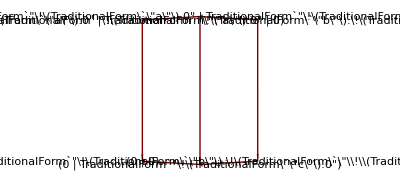

la semantica del processo Restr/(P|Q) e’ il grafo
	{{Restr/(R|S), dove R ∈ N_1 e S ∈ N_2}, 
		{Restr/(P|Q)⟶^labelRestr/R, dove P|Q⟶^labelR ∈ E_3 e label ∉ Restr} 
		∪ {Restr/(R|S)⟶^tauRestr/(T|V), dove R⟶^aT ∈ E e S⟶^(:a)V ∈ F e a∈Restr} 
		∪ {Restr/(R|S)⟶^tauRestr/(T|V), dove R⟶^(:a)T ∈ E e S⟶^aV ∈ F e a∈Restr}}
dove {N_1,E_1} e’ la semantica del processo P, {N_2,E_2} e’ la semantica del processo Q e {N_3,E_3} e’ la semantica del processo P|Q. La restrizione in combinazione con la composizione parallela serve per la comunicazione tra due processi. Ad esempio il processo a.0 prende a in input, mentre il processo :a.0 da a in output. Questi due processi possono comunicare tra di loro attraverso a. La semantica di {a}/(a.0|:a.0) e’ il grafo seguente

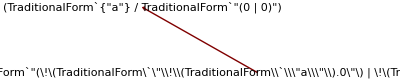

Da qui si capisce il significato di tau: quando un sistema fa una azione tau significa che due processi si sono scambiati un nome. 

Mostriamo anche un caso nel quale la comunicazione tra processi non avviene. La semantica di {a b}/(b.0|:c.0) e’ il grafo seguente

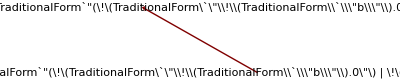

la semantica del processo Restr/P, se P non ha una composizione parallela al top level, e’ il grafo
	{{Restr/R, dove R ∈ N}, 
		{Restr/R⟶^aRestr/S, dove R⟶^aS ∈ E e a ∉ Restr}}
dove {N,E} e’ la semantica del processo P.  In questo caso la restrizione serve ad impedire ad un processo di fare un certo input o un certo output. Ad esempio la semantica del processo {a b}/(a.0+b.0+c.0) e’ il grafo seguente

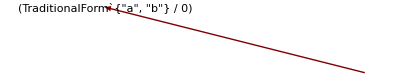

sia A un identificatore la cui definizione e’ A=P e sia {N,E} la semantica di P. Allora la semantica di A e’ quel grafo ottenuto da {N,E} dopo aver sostituito A a P. Ad esempio se un identificatore A e’ definito A=a.b.A allora la semantica di A e’ il grafo:

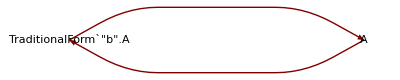

## Contenuto del package

### Generatore del grafo

La funzione getCcsGraph[process, definitions, iterationLimit] prende in input:
- process: una stringa che rappresenta un processo CCS
- definitions: una stringa che contiene una sequenza di definizioni di costanti. Le definizioni devono essere separate da un punto e virgola.
- iterationLimit: un intero che limita il numero di iterazioni dell’algoritmo.
La funzione restituisce in output un grafo che e’ la semantica del processo di input.

## Esempio di uso del package

Vediamo un esempio di un sistema distribuito modellato con CCS. Ci sono due processi: 
- un distributore automatico di caffe’ e the, di seguito indicato con l’identificatore CTM (Cofee Tee Machine)
- un cliente, di seguito indicato con l’identificatore Customer

La definizione del distributore automatico in CCS e’ 
				CTM = coin.:coffee.CTM + :tea.CTM
notiamo dalla definizione che il CTM si trova in uno stato iniziale in cui puo’ prendere in input una moneta (coin). Dopo che il CTM accetta una moneta, si trova in uno stato nel quale puo’ decidere di fare un caffe’ oppure un the. In questo semplice esempio e’ il distributore che decide se fare un the o un caffe’. Dopo che il distributore da in output una bevanda ritorna nel suo stato iniziale. La semantica di CTM e’ la seguente:

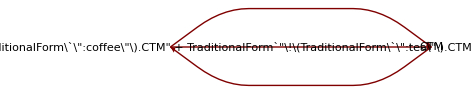

```mathematica
Needs["CcsTool`",NotebookDirectory[]<>"ccsTool.m"]
GraphPlot[
getCcsGraph[
"CTM", 
"CTM = coin.(:coffee.CTM + :tea.CTM)",
3
], 
DirectedEdges->True, 
VertexLabeling->All
]
```

La definizione in CCS che diamo di un possibile cliente e’ la seguente
				Customer= :coin.coffee.0
In questo modo modelliamo un cliente che inserisce una moneta e prende un caffe’. La semantica di Customer e’ la seguente:

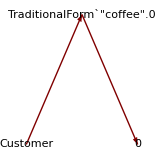

```mathematica
TreePlot[
getCcsGraph[
"Customer",
"Customer = :coin.coffee.0", 
3
], 
DirectedEdges->True, 
VertexLabeling->True
]
```

Modelliamo nel modo seguente il sistema cliente-distributore:
				{coin, coffee, tea}/(CTM|Customer)
La semantica del sistema e’ la seguente:

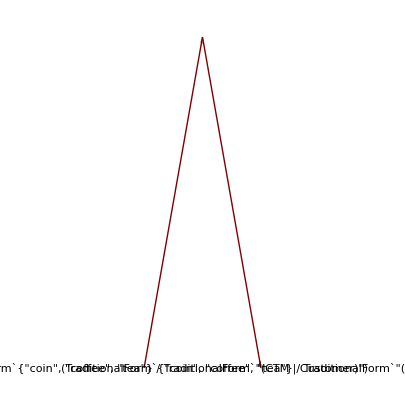

```mathematica
TreePlot[
getCcsGraph[
"{coin coffee tea}/(CTM|Customer)", "CTM = coin.(:coffee.CTM+:tea.CTM); Customer = :coin.(coffee.0)", 
5
], 
VertexLabeling->True, 
DirectedEdges->True
]
```

Lo stato iniziale del sistema e’ appunto 
				{coin, coffee, tea}/(CTM|Customer)
dalla semantica notiamo che il sistema in questo stato puo’ solo fare un’azione invisibile tau e arrivare in un altro stato 			
			{coin, coffee, tea}/((:coffee.CTM+:tea.CTM)  |  coffee.0)
questo e’ lo stato in cui si trova il sistema dopo che il cliente ha inserito una moneta nel distributore. Da questo stato abbiamo una sola transizione etichettata tau nello stato  	
				{coin, coffee, tea}/(CTM|0)
nel quale il cliente ha preso il suo caffe’ ed ha terminato l’esecuzione mentre il distributore e’ ritornato nel suo stato iniziale.

## References

[AIL07] L. Aceto, A. Ingolfsdottir, K. G. Larsen. Reactive Systems. Modelling, Specification and Verification. Cambridge University Press 2007

Il CCS e’ trattato anche nel corso MSC tenuto dal professor Roberto Gorrieri.